```mathematica
<<peeters`

peeters`setGitDir["../project/figures/phy487-qmsolids"]

fs=Style[#,FontSize->14]&;
```

peeters`

/Users/pjoot/project/figures/phy487-qmsolids

```mathematica
(*$Assumptions = a > 0 ;*)
Integrate[ 1/(a - u^2), {u, -Infinity, Infinity}]
```

ConditionalExpression[(a π)/(-a)^(3/2),Im[a]≠0||Re[a]≤0]

```mathematica
Clear[s]
s = Sum[ 1/(a - b^2 u^2), {u, -Infinity, Infinity}]  
s /. a -> "E" /. b -> ℏ^2/(2m) // TraditionalForm
```

(π Cot[(√a π)/b])/(√a b)

(2 π m cot((2 π √E m)/ℏ^2))/(√E ℏ^2)

WolframAlphaQueryResults

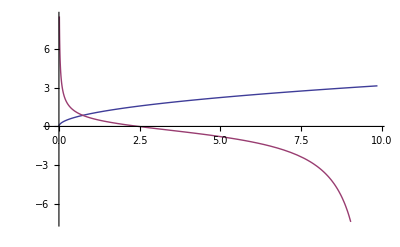

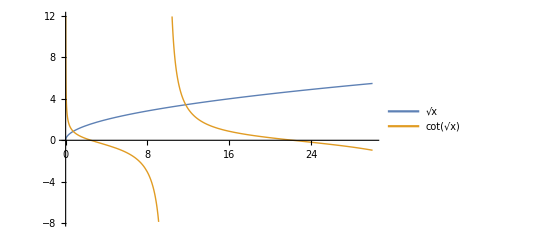

```mathematica
Clear[p]
p =Plot[{Sqrt[x], Cot[Sqrt[x]]}, {x, 0, 30}, 
PlotStyle -> Thick,
PlotLegends->Placed[fs/@{Sqrt[x], TraditionalForm[Cot[Sqrt[x]]]}, {Right, Bottom}]]
```

```mathematica
peeters`exportForLatex["ps7p2cFig1",p]
```

{ps7p2cFig1.eps,ps7p2cFig1pn.png}